## Sample from Gaussian distribution and construct .txt file to be read by ReACT

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bbose/Desktop/ML+ReACT

Models: wCDM, f(R), DGP and LCDM
Params:  omega_m, omega_b, H_0, n_s, sigma_8,  [fr0, omega_rc, {w0,wa}]  - Plancck best fits and 1sigma errors from : 1807.06209, 1910.09273 , 1605.03965, ReACT paper, Cataneo et al 2015.

```mathematica
mum = 0.3158;
sigm = 0.009;
mub = 0.0494;
sigb = 0.032;
muh0 = 67.32;
sigh0 = 0.41;
muns = 0.966;
signs = 0.007;
mus8 = 0.8120;
sigs8 = 0.0041;
mumg = 0;
sigfr0 = 10^(-5.5);
sigdgp = 0.173;
muw0 = -1;
sigw0 = 0.097;
muwa = 0;
sigwa = 0.32;
```

```mathematica
(*Generate Planck spectrum *)
mytab=TableForm[Table[{i,mum ,mub,muh0,muns,mus8,0.0000000000000001, muw0,muwa},{i,1,1}]]
Export["planck.txt",mytab,"Table","FieldSeparators"->" "];
```

1 | 0.3158 | 0.0494 | 67.32 | 0.966 | 0.812 | 1.×10^-16 | -1 | 0

```mathematica
myf[mu_,sig_]:=RandomVariate[NormalDistribution[mu,sig]]
```

```mathematica
mytab = Table[myf[muns,signs],{i,1,450}];
mytab2 = Table[myf[mub,sigb],{i,1,450}];
mytab3 = Table[Abs[myf[mumg,sigdgp]],{i,1,50000}];
mytab4 = Table[Abs[myf[mumg,sigfr0]],{i,1,50000}];
mytab5 = Table[Abs[myf[mus8,sigs8]],{i,1,50000}];
```

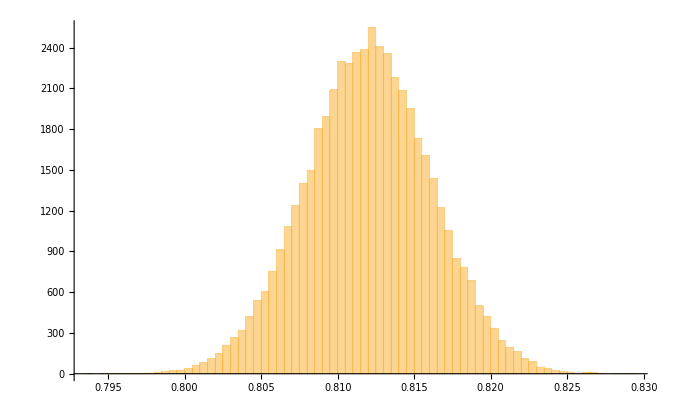

```mathematica
Histogram[{mytab5},100]
```

### Save parameters to myfile.txt for the 4 different classes considered

```mathematica
numberofsamp =  2500
```

2500

```mathematica
mytabwcdm=TableForm[Table[{i,myf[mum,sigm],Abs[myf[mub,sigb]],myf[muh0,sigh0],myf[muns,signs],myf[mus8,sigs8],myf[muw0,sigw0],myf[muwa,sigwa],1.},{i,1,numberofsamp}]];

mytabdgp=TableForm[Table[{i,myf[mum,sigm],Abs[myf[mub,sigb]],myf[muh0,sigh0],myf[muns,signs],myf[mus8,sigs8],Abs[myf[mumg,sigdgp]],1.,1.},{i,1,numberofsamp}]];

mytabfr=TableForm[Table[{i,myf[mum,sigm],Abs[myf[mub,sigb]],myf[muh0,sigh0],myf[muns,signs],myf[mus8,sigs8],Abs[myf[mumg,sigfr0]],1.,1.},{i,1,numberofsamp}]];

mytablcdm=TableForm[Table[{i,myf[mum,sigm],Abs[myf[mub,sigb]],myf[muh0,sigh0],myf[muns,signs],myf[mus8,sigs8],N[10^(-15)],1.,1.},{i,1,numberofsamp}]];
```

```mathematica
Export["myfile.txt",mytabfr,"Table","FieldSeparators"->" "];
```